```mathematica
Grid[{{a,b,c},{x,y,z}}]
```

a | b | c
x | y | z

```mathematica
Grid[{{a,b,c},{x,y^2,z^3}},Frame->All]
```

a | b | c
x | y^2 | z^3

```mathematica
Text[Grid[{{"first","second"},{"third","fourth"}}]]
```

first | second
third | fourth

```mathematica
data={{"first",1,2,3},{"second",11,5,6},{"third",111,8,9},{"fourth",1111,10,11}};
Text@Grid[Prepend[data,{"name","a","b","c"}],Background->{None,{Lighter[Yellow,.9],{White,Lighter[Blend[{Blue,Green}],.8]}}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->{{Left,Right,{Left}}},ItemSize->{{10,3,5,5}},Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

name | a | b | c
first | 1 | 2 | 3
second | 11 | 5 | 6
third | 111 | 8 | 9
fourth | 1111 | 10 | 11

```mathematica
Grid[{{100!},{50!}},ItemSize->Automatic,Frame->All]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000
30414093201713378043612608166064768844377641568960512000000000000

```mathematica
TabView[Tooltip[Show[CountryData[#,"Shape"],ImageSize->Tiny],#]-> DateListPlot[CountryData[#,{{"GDP"},{1970,2005}}],ImageSize->Medium]&/@CountryData["GroupOf10"]]
```

1234567891011

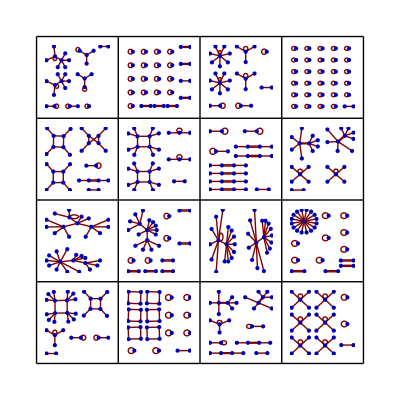

```mathematica
GraphicsGrid[Table[GraphPlot[Table[i->Mod[i^p,m],{i,m}]],{m,30,33},{p,2,5}],Frame->All]
```

```mathematica
Manipulate[Plot3D[Sinh[x+Cos[y+θ]],{x,-4,4},{y,-4,4},PlotStyle->color,Axes->axes,PerformanceGoal->"Quality"],{color,LightBlue},{θ,0,π},{axes,{True,False}}]
```

```mathematica
Manipulate[Plot3D[Sinh[x+Cosh[y+θ]],{x,-4,4},{y,-4,4},PlotStyle->color,Axes->axes,PerformanceGoal->"Speed"],{color,Green},{θ,0,π},{axes,{True,False}}]
```

```mathematica
Manipulate[RootLocusPlot[k (100 s (s+10))/((s+25) (s-10) (s^2-225)),{k,0,30},PlotRange->All,AspectRatio->1,PoleZeroMarkers->{Automatic,"ParameterValues"->kVal}],{kVal,0,30}]
```

```mathematica
PopupView[Table[Plot[BesselJ[n,x],{x,0,10}],{n,3}]]
```

```mathematica
DynamicModule[{pt={0,0}}, ClickPane[Dynamic@Graphics[{Blue,Disk[],Green,Point[pt]},ImageSize->Tiny],(pt=#)&]]
```

```mathematica
DynamicModule[{pt={0,0}},ClickPane[Framed@Graphics[{Blue,Dynamic@Disk[pt]},PlotRange->5],(pt=#)&]]
```

```mathematica
DynamicModule[{f={}},ClickPane[Framed@Dynamic@ParametricPlot[f,{t,0,10},PlotRange->100],(AppendTo[f,MatrixExp[({{-1.3,3},{-1.1,2}}) t].#])&]]
```

```mathematica
createCircle[{{x1_,y1_},{x2_,y2_},{x3_,y3_}}]:=With[{a=Det[({{x1,y1,1},{x2,y2,1},{x3,y3,1}})],d=-Det[({{x1^2+y1^2,y1,1},{x2^2+y2^2,y2,1},{x3^2+y3^2,y3,1}})],e=Det[({{x1^2+y1^2,x1,1},{x2^2+y2^2,x2,1},{x3^2+y3^2,x3,1}})],f=-Det[({{x1^2+y1^2,x1,y1},{x2^2+y2^2,x2,y2},{x3^2+y3^2,x3,y3}})]},Circle[{-(d/(2 a)),-(e/(2 a))},Sqrt[(d^2+e^2)/(4 a^2)-f/a]]]
createCircle[pts_]:={}
DynamicModule[{pts = {},c={}},ClickPane[Framed@Graphics[{Dynamic[c],Point[Dynamic[pts]]},PlotRange->Automatic],
(If[Length[pts]<3,AppendTo[pts,#],pts{#}];c=createCircle[pts])&]]
```